```mathematica
(*prior is a uniform on x between 0 and 1. Data is d=973 observations in which event is never seen*)
```

```mathematica
(*check that posterior distribution for x has been normalized correctly*)
```

```mathematica
Integrate[974 (1-x)^973,{x,0,1}]
```

1

```mathematica
(*maximum bound on 95% posterior estimate range for the frequency of off-diagonal
```

```mathematica
Solve[{Integrate[974 (1-x)^973,{x,0,max}]==0.95,0<max<1},max]
```

{{max→0.00307098}}

```mathematica
(*shape of posterior*)
```

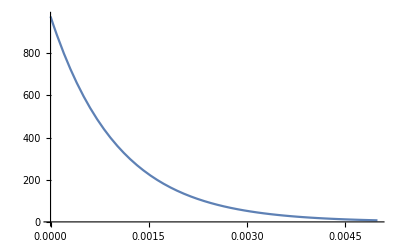

```mathematica
Plot[974 (1-x)^973,{x,0,0.005}]
```

```mathematica
(*check that posterior distribution for x has been normalized correctly*)
```

```mathematica
Integrate[3110 Binomial[2769+340,340] x^2769 (1-x)^340,{x,0,1}]
```

1

```mathematica
Solve[{NIntegrate[3110 Binomial[2769+340,340] x^2769 (1-x)^340,{x,0,max}]==0.975,0<max<1},max]
```

{{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.},{max→1.}}

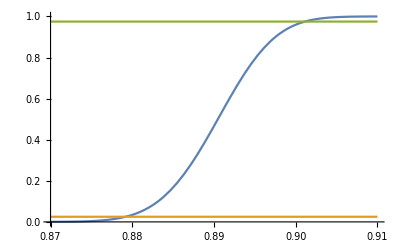

```mathematica
Plot[{NIntegrate[3110 Binomial[2769+340,340] x^2769 (1-x)^340,{x,0,max}],0.025,0.975},{max,0.87,0.91}]
```

```mathematica
340/(2769+340.)
```

0.10936

```mathematica
1-0.10935992280476037
```

0.89064

```mathematica
0.8906400771952396/0.003070975365048535
```

290.019